Power Tower Truss

```mathematica
w1=7;w2=11;h1=7;h2=12;
```

```mathematica
θ1=ArcTan[h2/w1];θ2=ArcTan[h1/w2];θ3=ArcTan[h1/w1];
```

```mathematica
r1=0.7;r2=0.9;
```

```mathematica
truss=Graphics[{Thick,
(*DRAWING TRUSS*)
{EdgeForm@Thick,FaceForm@None,Polygon[{{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2},{w1,h1+h2},{-w1,h1+h2}}]},
{Line[{{#*w1,h1+h2},{0,2*h1+h2}}],Line[{{#*w1,h2},{0,h1+h2}}],Line[{{#*w1,0},{0,h2}}]}&/@{-1,1},
Line[{{#,h1+h2},{#,0}}]&/@{-w1,w1},
Line[{{-w1,h2},{w1,h2}}],

{GrayLevel@0.7,
Disk[{-w1,-0.75},0.75],Polygon[{{-w1-0.75,-0.75/2},{-w1+0.75,-0.75/2},{-w1+1,-2.5},{-w1-1,-2.5}}],
Disk[{w1,-r1},r1],Polygon[{{w1-0.75,-0.75/2},{w1+0.75,-0.75/2},{w1+1,-2.5},{w1-1,-2.5}}],
Black,
Line[{{-w1+#*0.75,-0.75},{-w1+#,-2.5}}]&/@{-1,1},Line[{{-w1-1,-2.5},{-w1+1,-2.5}}],Line[{#,√(0.75^2-(#+w1)^2)-0.75}&/@Range[-w1-0.75,-w1+0.75,0.1]],
Line[{#,√(r1^2-(#-w1)^2)-r1}&/@Range[w1-0.997*r1,w1+0.997*r1,0.001]],
Line[{{w1+#*0.75,-0.75},{w1+#,-2.5}}]&/@{-1,1},Line[{{w1-1,-2.5},{w1+1,-2.5}}]}
},ImageSize->{600,400}];
```

```mathematica
labels=Graphics@{
Text[Framed[Style[Row@{" ",#1," "},16],RoundingRadius->15,FrameMargins->Tiny],#2,#3]&@@@{{"A",{-w1,0},{1.5,-1}},{"B",{w1,0},{-1.75,-1}},{"C",{w1,h2},{-1.5,0}},{"D",{w1,h1+h2},{-1.5,1}},{"E",{w1+w2,2*h1+h2},{-1,-1.2}},{"F",{0,2*h1+h2},{0,-1.2}},{"G",{-w1-w2,2*h1+h2},{1,-1.2}},{"H",{-w1,h1+h2},{1.5,1}},{" I ",{-w1,h2},{1.5,0}},{"J",{0,h1+h2},{0,-1.2}},{"K",{0,h2},{0,-1.2}}}};
```

```mathematica
Manipulate[
Module[{RAx,RBx,RBy,RAy,F3,F4,F6,F5,sol1,F14,F15,F2,F13,F7,F16,sol2,F12,F17,F10,F1,F9,F8,F11,F18,scale,colC,colT},
(*REACTION FORCES*)
RAx=0.5*(rax/.Solve[-rax+FEx==0,rax][[1]]);
RBx=RAx;
RBy=rb/.Solve[-2*w1*rb+(2*w1+w2)*FEy+(2*h1+h2)*FEx-w2*FG==0,rb][[1]];
RAy=ray/.Solve[ray+RBy-FEy-FG==0,ray][[1]];

(*MEMBER FORCES*)
(*joint G*)
F3=Chop[f3/.Solve[-f3*Sin[θ2]-FG==0,f3][[1]]];
F4=Chop[f4/.Solve[F3*Cos[θ2]+f4==0,f4][[1]]];

(*jointE*)
F6=Chop[f6/.Solve[-f6*Sin[θ2]-FEy==0,f6][[1]]];
F5=Chop[f5/.Solve[-f5-F6*Cos[θ2]+FEx==0,f5][[1]]];

(*joint F*)
sol1=Solve[{-f14*Sin[θ3]-f15*Sin[θ3]==0,-F4+F5-f14*Cos[θ3]+f15*Cos[θ3]==0},{f14,f15}][[1]];
F14=Chop[f14/.sol1];F15=Chop[f15/.sol1];

(*joint H*)
F2=Chop[f2/.Solve[-f2+F3*Sin[θ2]+F14*Sin[θ3]==0,f2][[1]]];
F13=Chop[f13/.Solve[-F3*Cos[θ2]+f13+F14*Cos[θ3]==0,f13][[1]]];

(*joint D*)
F7=Chop[f7/.Solve[F6*Sin[θ2]-f7+F15*Sin[θ3]==0,f7][[1]]];
F16=Chop[f16/.Solve[F6*Cos[θ2]-F15*Cos[θ3]-f16==0,f16][[1]]];

(*joint J*)
sol2=Solve[{-f12*Sin[θ3]-f17*Sin[θ3]==0,-f12*Cos[θ3]-F13+F16+f17*Cos[θ3]==0},{f12,f17}][[1]];
F12=Chop[f12/.sol2];F17=Chop[f17/.sol2];

(*joint A*)
F10=Chop[f10/.Solve[f10*Cos[θ1]-RAx==0,f10][[1]]];
F1=Chop[f1/.Solve[f1+F10*Sin[θ1]+RAy==0,f1][[1]]];

(*joint B*)
F9=Chop[f9/.Solve[-f9*Cos[θ1]-RBx==0,f9][[1]]];
F8=Chop[f8/.Solve[f8+F9*Sin[θ1]+RBy==0,f8][[1]]];

(*joint I*)
F11=Chop[f11/.Solve[f11+F12*Cos[θ3]==0,f11][[1]]];

(*joint C*)
F18=Chop[f18/.Solve[-F17*Cos[θ3]-f18==0,f18][[1]]];

scale[F_]:=3+10*Rescale[Abs@F,{0,25.7}];
colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Show[truss,If[label,labels,{}],PlotRange->{{-22,30},{-15,31.2}},Epilog->{
Flatten@{Thickness@0.007,Which[#1<0,{colC,Arrowheads@{-0.05,0.05}},#1>0,{colT,Arrowheads@{{0.05,0.315},{-0.05,0.675}}},#1==0,Black],If[#1==0,Line,Arrow]@#2}&@@@{
{F1,{{-w1,0},{-w1,h2}}},{F2,{{-w1,h2},{-w1,h1+h2}}},{F3,{{-w1,h1+h2},{-w1-w2,2*h1+h2}}},{F4,{{-w1-w2,2*h1+h2},{0,2*h1+h2}}},{F5,{{0,2*h1+h2},{w1+w2,2*h1+h2}}},{F6,{{w1,h1+h2},{w1+w2,2*h1+h2}}},{F7,{{w1,h2},{w1,h1+h2}}},{F8,{{w1,0},{w1,h2}}},{F9,{{w1,0},{0,h2}}},{F10,{{-w1,0},{0,h2}}},{F11,{{-w1,h2},{0,h2}}},{F12,{{-w1,h2},{0,h1+h2}}},{F13,{{-w1,h1+h2},{0,h1+h2}}},{F14,{{-w1,h1+h2},{0,2*h1+h2}}},{F15,{{w1,h1+h2},{0,2*h1+h2}}},{F16,{{0,h1+h2},{w1,h1+h2}}},{F17,{{w1,h2},{0,h1+h2}}},{F18,{{w1,h2},{0,h2}}}},

Text[Rotate[Style[If[#1==0,0,NumberForm[N@Abs@#1,{5,If[Abs@#1<10,2,1]}]],17,Which[#1<0,colC,#1>0,colT,#1==0,Black],Background->White],#4],#3]&@@@{{F1,"1,AI",{-w1,h2/2},π/2},{F2,"6,HI",{-w1,h2+h1/2},π/2},{F3,"3,GH",{-w1-w2/2,1.5*h1+h2},-θ2},{F4,"3,FG",{-(w1+w2)/2,2*h1+h2},0},{F5,"4,EF",{(w1+w2)/2,2*h1+h2},0},{F6,"4,DE",{w1+0.5*w2,1.5*h1+h2},θ2},{F7,"7,CD",{w1,0.5*h1+h2},π/2},{F8,"2,BC",{w1,0.5h2},π/2},{F9,"2,BK",{0.5*w1,h2/2},-θ1},{F10,"1,AK",{-0.5*w1,0.5*w2},θ1},{F11,"9,IK",{-0.5*w1,h2},0},{F12,"9,IJ",{-0.5*w1,0.5*h1+h2},θ3},{F13,"6,HJ",{-0.5*w1,h1+h2},0},{F14,"5,FH",{-0.5*w1,1.5*h1+h2},θ3},{F15,"5,DF",{0.5*w1,1.5*h1+h2},-θ3},{F16,"7,DJ",{0.5*w1,h1+h2},0},{F17,"8,CJ",{0.5*w1,0.5*h1+h2},-θ3},{F18,"8,CK",{0.5*w1,h2},0}},

{Blue,Thickness@0.01,Arrowheads@0.05,
Arrow[{{-(w1+w2),2*h1+h2},{-(w1+w2),2*h1+h2-scale[FG]}}],
Arrow[{{w1+w2,2*h1+h2},{w1+w2,2*h1+h2-scale[FEy]}}],
If[FEx≠0,Arrow[{{w1+w2,2*h1+h2},{w1+w2+scale[FEx],2*h1+h2}}]],
Arrow[If[RAy<0,Reverse,N]@{{-w1,-0.75-scale[RAy]},{-w1,-0.75}}],If[RAx≠0,Arrow[{{-w1,-0.1*h1},{-w1-scale[RAx],-0.1*h1}}]],
If[RBx≠0,Arrow[{{w1,-0.1*h1},{w1-scale[RBx],-0.1*h1}}]],
Arrow[{{w1,-0.75-scale[RBy]},{w1,-0.1*h1}}],
Text[Style[If[label,Subscript[Style["F",Italic],"G"],Row@{NumberForm[Abs@FG,{5,2}]," kN"}],18],{-w1-w2,2*h1+h2-scale[FG]},{0,1.5}],
Text[Style[If[label,Subscript[Style["F",Italic],Row@{"E,",Style[#2,Italic]}],Row@{NumberForm[Abs@#1,{5,2}]," kN"}],18],#3,#4]&@@@{
{FEy,"y",{w1+w2,2*h1+h2-scale[FEy]},{0,1.5}},If[FEx≠0,{FEx,"x",{w1+w2+scale[FEx],2*h1+h2},{-1.2,0}}]},
Text[Style[If[label,Subscript[Style["R",Italic],Row@{"A,",Style[#2,Italic]}],Row@{NumberForm[N@Abs@#1,{5,2}]," kN"}],18],#3,#4]&@@@{
If[RAx≠0,{RAx,"x",{-w1-scale[RAx],-0.75},{1.2,0}}],{RAy,"y",{-w1,-0.75-scale[RAy]},{0,1.5}}},
Text[Style[If[label,Subscript[Style["R",Italic],Row@{"B,",Style[#2,Italic]}],Row@{NumberForm[N@Abs@#1,{5,2}]," kN"}],18],#3,#4]&@@@{If[RBx≠0,{RBx,"x",{w1-scale[RBx],-0.1*h1},{1.2,0}}],{RBy,"y",{w1,-0.75-scale[RBy]},{0,1.5}}}},

{PointSize@0.02,Point@#,White,PointSize@0.012,Point@#}&/@{{-w1,-0.75},{-w1,h2},{-w1,h1+h2},{-w1-w2,2*h1+h2},{w1,-0.75},{w1,h2},{w1,h1+h2},{w1+w2,2*h1+h2},{0,h2},{0,h1+h2},{0,2*h1+h2}},

Text[Style[Row@{"all ",Style["compression",colC]," and ",Style["tension",colT]," forces are in kN"},17,GrayLevel@0.4],{0,30.5}]
}]
],
Grid[{
{"forces at joint E (kN)",
Control[{{FEx,4,Row@{"horizontal ",Subscript[Style["F",Italic],Row@{"E,",Style["x",Italic]}]}},0,4,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{FEy,8,Row@{"vertical ",Subscript[Style["F",Italic],Row@{"E,",Style["y",Italic]}]}},4,10,0.1,Appearance->"Labeled",ImageSize->Small}]},
{Control[{{FG,5,"force at joint G (kN)"},4,10,0.1,Appearance->"Labeled"}],SpanFromLeft,
Control[{{label,False,"show joint labels"},{True,False}}]}
},Alignment->Left],
SaveDefinitions->True]
```

The method of joints is used to solve for the member forces and reaction forces on a power tower truss. Use sliders to set the point load forces at joints G and E, and check "show joint labels" to see the labeled joints. This truss rests on two pinned supports, which resist both vertical and horizontal forces. Member forces are shown in kN. Arrows that point outward (green) represent the member response to compression forces, and arrows that point inward (red) represent the member response to tension forces. Compression acts to shorten the member and tension acts to lengthen the member. Zero members (black lines) are in neither tension nor compression, so their force is 0 kN. Zero members provide stability and extra support to the structure in case another member fails.

The reaction forces are calculated first by summing the x-forces, then calculating moments about joint G, and the doing a force balance in the y-direction.

∑F_x=0=-R_(A,x)-R_(B,x)+F_(E,x),

∑M_A=0=-2 w_1 R_(B,y)+(2 w_1+w_2) F_(E,y)+(2 h_1+h_2) F_(E,x)-w_2 F_G,

∑F_y=0=R_(A,y)+R_(B,y)-F_G-F_(E,y),

where R_(A,x) and R_(A,y) are the reaction forces in the x and y directions at joint A, R_(B,x) and R_(B,y) are the reaction forces at joint B, R_(A,x)=R_(B,x)=1/2 F_(E,x), F_(E,x) and F_(E,y) are the point load forces in the x and y directions at joint E, F_G is the point load force at joint G, w_1 and w_2 are the shorter and longer widths, and h_1 and h_2 are the shorter and longer heights. The second and third terms ((2 w_1+w_2) F_(E,y), (2 h_1+h_2) F_(E,x)) are positive in the moment balance because they cause a clockwise rotation, and the first and fourth terms (-2 w_1 R_B, -w_2 F_G) are negative because they cause a counterclockwise rotation.

The method of joints is used to calculate the member forces using the order of the calculations below. Force balances are done assuming we can determine which forces are under tension and which forces are under compression prior to solving the truss. At joint A there is an upward force of R_(A,y) so we know that F_1 must be a compression force in order for the truss to remain stationary. Also, there is a force of R_(A,x) in the negative x direction so F_10 must be a tension force. A labeled truss is shown in Figure 1 below. See the angles used in Figure 2.

Joint G:
θ_2=tan^-1(h_1/w_2),
∑F_y=0=F_3 sin θ_2-F_G,
∑F_x=0=-F_3 cos θ_2+F_4.

Joint E:

∑F_y=0=F_6 sin θ_2-F_(E,y),

∑F_x=0=-F_5+F_6 cos θ_2+F_(E,x).

Joint F:

θ_3=tan^-1(h_1/w_1),

∑F_y=0=-F_14 sin θ_3+F_15 sin θ_3,

∑F_x=0=-F_4+F_5-F_14 cos θ_3-F_15 cos θ_3.

Joint H:

∑F_x=0=F_3 cos θ_2-F_13+F_14 cos θ_3,

∑F_y=0=F_2-F_3 sin θ_2+F_14 sin θ_3.

Joint D:

∑F_x=0=-F_6 cos θ_2+F_15 cos θ_3+F_16,

∑F_y=0=-F_6 sin θ_2+F_7-F_15 sin θ_3.

Joint J:

∑F_x=0=-F_12 cos θ_3+F_13-F_16-F_17 cos θ_3,

∑F_y=0=-F_12 sin θ_3+F_17 sin θ_3.

Joint A:

θ_1=tan^-1(h_2/w_1),

∑F_x=0=F_10 cos θ_1-R_(A,x),

∑F_y=0=-F_1+F_10 sin θ_1+R_(A,y).

Joint B:

∑F_x=0=F_9 cos θ_1-R_(B,x),

∑F_y=0=-F_8+F_9 sin θ_1+R_(B,y).

Joint I:

∑F_x=0=-F_11+F_12 cos θ_3.

Joint C:

∑F_x=0=F_17 cos θ_3-F_18.

Figure 1

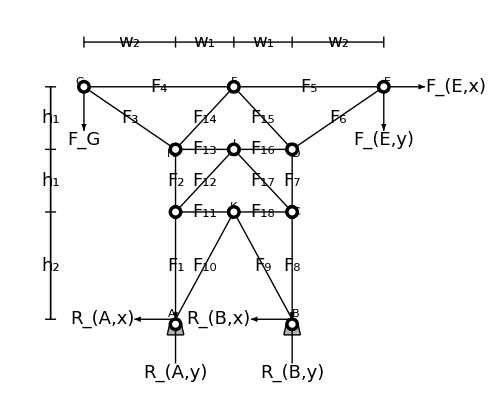

For some conditions F_14 is under compression and F_15 is under tension.

Figure 2

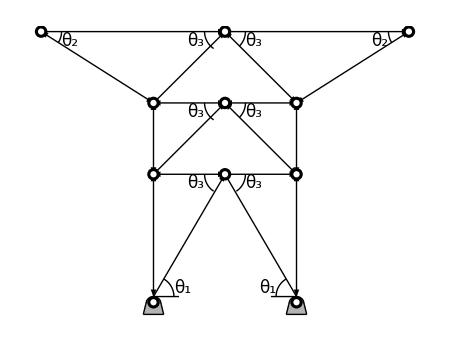

Reference

[1] Engineering Mechanics Statics 12th ed., New Jersey: Pearson Education Inc., 2010.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

mechanical engineering

civil engineering

statics

mechanics

method of joints

truss

member forces

compression force

tension force

zero member

Contributed by: Rachael L. Baumann

Additional contributions by: John L. Falconer

(University of Colorado Boulder, Department of Chemical and Biological Engineering)